# Fisher estimates for a power law mass spectrum

```mathematica
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

## No selection effects

## Inputs

```mathematica
$Assumptions={θ>0,θmax>0,θmin>0,θmax>θmin, σ>0 & σ<1000,λ>-1}
```

{θ>0,θmax>0,θmin>0,θmax>θmin,σ (σ>0&)<1000,λ>-1}

In this first example we do not consider selection effects, meaning we set the probability of detection for both source and population parameters to one.

```mathematica
pdetθ[M_]:=1
pdetλ[λ_]:=1
ppop[{θ_,θmin_,θmax_},λ_]:= λ/(θmax^λ-θmin^λ) θ^(λ-1)
```

We check here that the population model is correctly normalized.

```mathematica
Integrate[ppop[{θ,θmin,θmax},λ],{θ,θmin,θmax}]
```

1

A bunch of useful quantities that enter the Fisher matrix.

```mathematica
Γ = 1/σ^2;  (* True only in the case in which d = θ + noise. *)
Dmij= Γ ;  (* Only true in the absence of selection effects. *)
Dmi = D[pdetθ[θ],θ];
P = D[Log@ppop[{θ,θmin,θmax},λ],θ];
H = - D[D[Log@ppop[{θ,θmin,θmax},λ],θ],θ];
```

Choose the true parameters here.

```mathematica
λtrue =0.00001;
truepars ={Nobs->1000,λ->λtrue,σ->0.1,θmax->10^7, θmin->10^4}//N;
```

## Fisher matrix and precision estimates [only retaining first term]

In this simplified scenario, we only consider the first (dominant) contribution to the Fisher matrix, without considering selection effects.
Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
SimpPopFisherNoSelectionEffects[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=
Integrate[(1/ppop[{θ,θmin,θmax},λ])D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,θmin,θmax}]
```

```mathematica
ΓλλSimpNoSelectionEffects = SimpPopFisherNoSelectionEffects[λ,{M,Mmin,Mmax},{λ,λ}];//Timing
```

{211.338,Null}

```mathematica
√(1/(Nobs*ΓλλSimpNoSelectionEffects))
Δα =%/.{Mmax->θmax, Mmin->θmin}/.truepars
```

√(1/(Nobs (1/λ^2-(Mmax^λ Mmin^λ (Log[Mmax]-Log[Mmin])^2)/((Mmax^λ-Mmin^λ)^2))))

0.0157423

Below we find the InputForm of the the analytical expressions below, which is used then parsed into Python with simpy.

```mathematica
√(1/(Nobs*ΓλλSimpNoSelectionEffects))/.λ->alpha//InputForm
```

Sqrt[1/(Nobs*(alpha^(-2) - (Mmax^alpha*Mmin^alpha*(Log[Mmax] - Log[Mmin])^2)/
     (Mmax^alpha - Mmin^alpha)^2))]

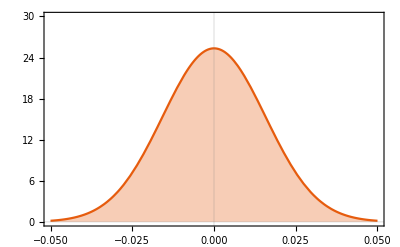

```mathematica
SimplifiedFisher=Plot[
PDF[NormalDistribution[λtrue,Δα],x]//Evaluate,{x,-.05,.05},
Filling->Axis,PlotRange->{All,{0,30}},
FrameLabel->{{MaTeX["\\text{PDF}",FontSize->17],None},{MaTeX["\\alpha_0",FontSize->17],None}},
FrameTicksStyle->Directive[Black,13],
TicksStyle->Directive[Black,AbsoluteThickness[100]],
PlotTheme-> "Scientific", 
Frame->True]
```

## Fisher matrix and precision estimates [including all terms]

The investigation here is aimed at showing that the first term in the Fisher matrix is the one dominating. 
This can also be seen in the Python notebooks.

Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
Γλλ=With[{θmin =10^4 ,θmax = 10^7,Γ = Γ, H = H, D2 = Dmij,D1=Dmi},
model = ppop[{θ,θmin,θmax},λ];
a = Integrate[(pdetθ[θ]/(model pdetλ[λ]))D[model,λ]*D[model,λ],{θ,θmin,θmax}];
b = - 1/pdetλ[λ]^2 D[pdetλ[λ],λ]*D[pdetλ[λ],λ];
c = 1/2 Integrate[D[D[Log@(Γ+H),λ],λ] pdetθ[θ]/pdetλ[λ] model,{θ,θmin,θmax}];
d =-1/2 Integrate[D[D[(Γ+H)^-1,λ],λ]D2 model/pdetλ[λ],{θ,θmin,θmax}];
e =- Integrate[D[D[P(Γ+H)^-1,λ],λ]D1 model/pdetλ[λ],{θ,θmin,θmax}];
f = -Integrate[D[D[P^2(Γ+H)^-1,λ],λ] model/pdetλ[λ],{θ,θmin,θmax}];
a+b+c+d+e+f
];//Timing
```

{71.5564,Null}

```mathematica
√(1/(Nobs*Γλλ));
%/.truepars/.{θmin ->10^4 ,θmax -> 10^7}
Δαfull=Re[%]
```

0.0158814+8.87709×10^-10 ⅈ

0.0158814

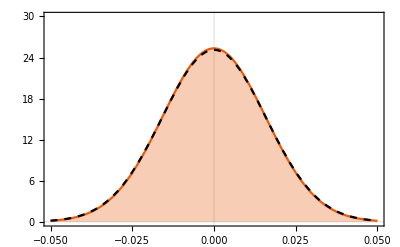

```mathematica
FullFisher = Plot[PDF[NormalDistribution[λtrue,Δαfull],x]//Evaluate,{x,-.05,.05},PlotStyle->{Black,Dashed}];
Show[SimplifiedFisher,FullFisher]
```

## Helpful expressions for the case with selection effects

## Inputs

The aim here is not to calculate the expression analytically, as it would be too hard to do. 
We instead help the numerical integration in Python by obtaining some analytical expressions that are valid for the specific case of a power law distribution.

```mathematica
$Assumptions={σ>0};
```

```mathematica
σθ=1/2 Erfc[(dth-θ)/(√2 √(σ^2))]; 
pθλ = ppop[{θ,θmin,θmax},λ];
```

```mathematica
Dm1 = D[σθ,θ];
Dm2 = Γ;
Hij=-D[D[pθλ,θ],θ];
Pj = D[Log@pθλ,θ];
```

```mathematica
somepars={θmin->10^4,θmax->10^7};
```

The FM expression can be written as int of function of θ times p(θ|λ), integrated over θ, which can be treated with Monte Carlo methods by drawing samples from p(θ|λ) and using them as input for the function of θ. Below are the expressions needed for such a function of θ.

The details can be found in the jupyter notebook with notes on how the Fisher Matrix is actually calculated. Here we only retrieve the InputForm of the integrands, as specified there. The expressions obtained here are then inserted in the pickled dictionary.

```mathematica
firstarg=-D[D[Log[pθλ/pλ[λ]],λ],λ]/.{θmax->Mmax, θmin->Mmin,λ->alpha,pλ[λ]->selfct, pλ'[λ]->derselfct, pλ''[λ]->dderselfct}//FullSimplify;
Framed@firstarg
firstarg//InputForm
```

1/alpha^2+(-derselfct^2+dderselfct selfct)/selfct^2-(Mmax^alpha Mmin^alpha (Log[Mmax]-Log[Mmin])^2)/((Mmax^alpha-Mmin^alpha)^2)

alpha^(-2) + (-derselfct^2 + dderselfct*selfct)/selfct^2 - 
 (Mmax^alpha*Mmin^alpha*(Log[Mmax] - Log[Mmin])^2)/(Mmax^alpha - Mmin^alpha)^2

```mathematica
secondarg = 1/2 D[D[Log[Γ + Hij],λ],λ]/.{θ->lnM,λ->alpha, σ->sigma, θmax->Mmax, θmin->Mmin}//FullSimplify;//Timing
Framed@secondarg
secondarg//InputForm
```

{18.9336,Null}

(lnM^(-6+alpha) (-lnM^alpha ((2+3 (-2+alpha) alpha) (Mmax^alpha-Mmin^alpha)+(-2+alpha) (-1+alpha) alpha (Mmax^alpha (Log[lnM]-Log[Mmax])+Mmin^alpha (-Log[lnM]+Log[Mmin])))^2-1/sigma^2 lnM^3 (Mmax^alpha-Mmin^alpha-(-2+alpha) (-1+alpha) alpha lnM^(-3+alpha) sigma^2) (6 (-1+alpha) (Mmax^alpha-Mmin^alpha)^2+Mmax^(2 alpha) (4+6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[lnM]-Log[Mmax])) (Log[lnM]-Log[Mmax])+Mmin^(2 alpha) (4+6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[lnM]-Log[Mmin])) (Log[lnM]-Log[Mmin])+Mmax^alpha Mmin^alpha (-2 (-2+alpha) (-1+alpha) alpha Log[lnM]^2+4 (Log[Mmax]+Log[Mmin])+2 Log[lnM] (-4-6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[Mmax]+Log[Mmin]))+(-2+alpha) alpha ((-1+alpha) Log[Mmax]^2+Log[Mmax] (6-4 (-1+alpha) Log[Mmin])+Log[Mmin] (6+(-1+alpha) Log[Mmin]))))))/(2 (Mmax^alpha-Mmin^alpha)^4 (((-2+alpha) (-1+alpha) alpha lnM^(-3+alpha))/(-Mmax^alpha+Mmin^alpha)+1/sigma^2)^2)

(lnM^(-6 + alpha)*(-(lnM^alpha*((2 + 3*(-2 + alpha)*alpha)*(Mmax^alpha - Mmin^alpha) + 
       (-2 + alpha)*(-1 + alpha)*alpha*(Mmax^alpha*(Log[lnM] - Log[Mmax]) + 
         Mmin^alpha*(-Log[lnM] + Log[Mmin])))^2) - 
   (lnM^3*(Mmax^alpha - Mmin^alpha - (-2 + alpha)*(-1 + alpha)*alpha*lnM^(-3 + alpha)*sigma^2)*
     (6*(-1 + alpha)*(Mmax^alpha - Mmin^alpha)^2 + Mmax^(2*alpha)*(4 + 6*(-2 + alpha)*alpha + 
        (-2 + alpha)*(-1 + alpha)*alpha*(Log[lnM] - Log[Mmax]))*(Log[lnM] - Log[Mmax]) + 
      Mmin^(2*alpha)*(4 + 6*(-2 + alpha)*alpha + (-2 + alpha)*(-1 + alpha)*alpha*
         (Log[lnM] - Log[Mmin]))*(Log[lnM] - Log[Mmin]) + Mmax^alpha*Mmin^alpha*
       (-2*(-2 + alpha)*(-1 + alpha)*alpha*Log[lnM]^2 + 4*(Log[Mmax] + Log[Mmin]) + 
        2*Log[lnM]*(-4 - 6*(-2 + alpha)*alpha + (-2 + alpha)*(-1 + alpha)*alpha*
           (Log[Mmax] + Log[Mmin])) + (-2 + alpha)*alpha*((-1 + alpha)*Log[Mmax]^2 + 
          Log[Mmax]*(6 - 4*(-1 + alpha)*Log[Mmin]) + Log[Mmin]*(6 + (-1 + alpha)*Log[Mmin])))))/
    sigma^2))/(2*(Mmax^alpha - Mmin^alpha)^4*
  (((-2 + alpha)*(-1 + alpha)*alpha*lnM^(-3 + alpha))/(-Mmax^alpha + Mmin^alpha) + sigma^(-2))^2)

```mathematica
thirdarg =- 1/2 D[D[(Γ + Hij)^-1,λ],λ]Dm2/.{θ->lnM,λ->alpha, σ->sigma, θmax->Mmax, θmin->Mmin}//FullSimplify;//Timing
Framed@thirdarg
thirdarg//InputForm
```

{25.6183,Null}

-((lnM^(-6+alpha) (2 lnM^alpha ((2+3 (-2+alpha) alpha) (Mmax^alpha-Mmin^alpha)+(-2+alpha) (-1+alpha) alpha (Mmax^alpha (Log[lnM]-Log[Mmax])+Mmin^alpha (-Log[lnM]+Log[Mmin])))^2+1/sigma^2 lnM^3 (Mmax^alpha-Mmin^alpha-(-2+alpha) (-1+alpha) alpha lnM^(-3+alpha) sigma^2) (6 (-1+alpha) (Mmax^alpha-Mmin^alpha)^2+Mmax^(2 alpha) (4+6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[lnM]-Log[Mmax])) (Log[lnM]-Log[Mmax])+Mmin^(2 alpha) (4+6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[lnM]-Log[Mmin])) (Log[lnM]-Log[Mmin])+Mmax^alpha Mmin^alpha (-2 (-2+alpha) (-1+alpha) alpha Log[lnM]^2+4 (Log[Mmax]+Log[Mmin])+2 Log[lnM] (-4-6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[Mmax]+Log[Mmin]))+(-2+alpha) alpha ((-1+alpha) Log[Mmax]^2+Log[Mmax] (6-4 (-1+alpha) Log[Mmin])+Log[Mmin] (6+(-1+alpha) Log[Mmin]))))))/(2 (Mmax^alpha-Mmin^alpha)^4 (((-2+alpha) (-1+alpha) alpha lnM^(-3+alpha))/(-Mmax^alpha+Mmin^alpha)+1/sigma^2)^3 sigma^2))

-1/2*(lnM^(-6 + alpha)*(2*lnM^alpha*((2 + 3*(-2 + alpha)*alpha)*(Mmax^alpha - Mmin^alpha) + 
       (-2 + alpha)*(-1 + alpha)*alpha*(Mmax^alpha*(Log[lnM] - Log[Mmax]) + 
         Mmin^alpha*(-Log[lnM] + Log[Mmin])))^2 + 
    (lnM^3*(Mmax^alpha - Mmin^alpha - (-2 + alpha)*(-1 + alpha)*alpha*lnM^(-3 + alpha)*sigma^2)*
      (6*(-1 + alpha)*(Mmax^alpha - Mmin^alpha)^2 + Mmax^(2*alpha)*(4 + 6*(-2 + alpha)*alpha + 
         (-2 + alpha)*(-1 + alpha)*alpha*(Log[lnM] - Log[Mmax]))*(Log[lnM] - Log[Mmax]) + 
       Mmin^(2*alpha)*(4 + 6*(-2 + alpha)*alpha + (-2 + alpha)*(-1 + alpha)*alpha*
          (Log[lnM] - Log[Mmin]))*(Log[lnM] - Log[Mmin]) + Mmax^alpha*Mmin^alpha*
        (-2*(-2 + alpha)*(-1 + alpha)*alpha*Log[lnM]^2 + 4*(Log[Mmax] + Log[Mmin]) + 
         2*Log[lnM]*(-4 - 6*(-2 + alpha)*alpha + (-2 + alpha)*(-1 + alpha)*alpha*
            (Log[Mmax] + Log[Mmin])) + (-2 + alpha)*alpha*((-1 + alpha)*Log[Mmax]^2 + 
           Log[Mmax]*(6 - 4*(-1 + alpha)*Log[Mmin]) + Log[Mmin]*(6 + (-1 + alpha)*Log[Mmin])))))/
     sigma^2))/((Mmax^alpha - Mmin^alpha)^4*
   (((-2 + alpha)*(-1 + alpha)*alpha*lnM^(-3 + alpha))/(-Mmax^alpha + Mmin^alpha) + sigma^(-2))^3*
   sigma^2)

```mathematica
fourtharg =- D[D[Pj(Γ + Hij)^-1,λ],λ]Dm1/.{θ->lnM,λ->alpha, σ->sigma, θmax->Mmax, θmin->Mmin,ⅇ^(-(dth-lnM)^2/(2 sigma^2))->Exp[-(dth-lnM)^2/(2 sigma^2)]}//FullSimplify;//Timing
Framed@fourtharg
fourtharg//InputForm
```

{0.355569,Null}

(ⅇ^(-(dth-lnM)^2/(2 sigma^2)) lnM^(-7+alpha) (2 (Mmax^alpha-Mmin^alpha) (lnM^3 (-Mmax^alpha+Mmin^alpha)+(-2+alpha) (-1+alpha) alpha lnM^alpha sigma^2) ((2+3 (-2+alpha) alpha) (Mmax^alpha-Mmin^alpha)+(-2+alpha) (-1+alpha) alpha (Mmax^alpha (Log[lnM]-Log[Mmax])+Mmin^alpha (-Log[lnM]+Log[Mmin])))+2 (1-alpha) lnM^alpha sigma^2 ((2+3 (-2+alpha) alpha) (Mmax^alpha-Mmin^alpha)+(-2+alpha) (-1+alpha) alpha (Mmax^alpha (Log[lnM]-Log[Mmax])+Mmin^alpha (-Log[lnM]+Log[Mmin])))^2+(1-alpha) lnM^3 (Mmax^alpha-Mmin^alpha-(-2+alpha) (-1+alpha) alpha lnM^(-3+alpha) sigma^2) (6 (-1+alpha) (Mmax^alpha-Mmin^alpha)^2+Mmax^(2 alpha) (4+6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[lnM]-Log[Mmax])) (Log[lnM]-Log[Mmax])+Mmin^(2 alpha) (4+6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[lnM]-Log[Mmin])) (Log[lnM]-Log[Mmin])+Mmax^alpha Mmin^alpha (-2 (-2+alpha) (-1+alpha) alpha Log[lnM]^2+4 (Log[Mmax]+Log[Mmin])+2 Log[lnM] (-4-6 (-2+alpha) alpha+(-2+alpha) (-1+alpha) alpha (Log[Mmax]+Log[Mmin]))+(-2+alpha) alpha ((-1+alpha) Log[Mmax]^2+Log[Mmax] (6-4 (-1+alpha) Log[Mmin])+Log[Mmin] (6+(-1+alpha) Log[Mmin]))))))/((Mmax^alpha-Mmin^alpha)^4 √(2 π) (((-2+alpha) (-1+alpha) alpha lnM^(-3+alpha))/(-Mmax^alpha+Mmin^alpha)+1/sigma^2)^3 (sigma^2)^(3/2))

(lnM^(-7 + alpha)*(2*(Mmax^alpha - Mmin^alpha)*(lnM^3*(-Mmax^alpha + Mmin^alpha) + 
     (-2 + alpha)*(-1 + alpha)*alpha*lnM^alpha*sigma^2)*
    ((2 + 3*(-2 + alpha)*alpha)*(Mmax^alpha - Mmin^alpha) + (-2 + alpha)*(-1 + alpha)*alpha*
      (Mmax^alpha*(Log[lnM] - Log[Mmax]) + Mmin^alpha*(-Log[lnM] + Log[Mmin]))) + 
   2*(1 - alpha)*lnM^alpha*sigma^2*((2 + 3*(-2 + alpha)*alpha)*(Mmax^alpha - Mmin^alpha) + 
      (-2 + alpha)*(-1 + alpha)*alpha*(Mmax^alpha*(Log[lnM] - Log[Mmax]) + 
        Mmin^alpha*(-Log[lnM] + Log[Mmin])))^2 + (1 - alpha)*lnM^3*
    (Mmax^alpha - Mmin^alpha - (-2 + alpha)*(-1 + alpha)*alpha*lnM^(-3 + alpha)*sigma^2)*
    (6*(-1 + alpha)*(Mmax^alpha - Mmin^alpha)^2 + Mmax^(2*alpha)*(4 + 6*(-2 + alpha)*alpha + 
       (-2 + alpha)*(-1 + alpha)*alpha*(Log[lnM] - Log[Mmax]))*(Log[lnM] - Log[Mmax]) + 
     Mmin^(2*alpha)*(4 + 6*(-2 + alpha)*alpha + (-2 + alpha)*(-1 + alpha)*alpha*(Log[lnM] - Log[Mmin]))*
      (Log[lnM] - Log[Mmin]) + Mmax^alpha*Mmin^alpha*(-2*(-2 + alpha)*(-1 + alpha)*alpha*Log[lnM]^2 + 
       4*(Log[Mmax] + Log[Mmin]) + 2*Log[lnM]*(-4 - 6*(-2 + alpha)*alpha + 
         (-2 + alpha)*(-1 + alpha)*alpha*(Log[Mmax] + Log[Mmin])) + 
       (-2 + alpha)*alpha*((-1 + alpha)*Log[Mmax]^2 + Log[Mmax]*(6 - 4*(-1 + alpha)*Log[Mmin]) + 
         Log[Mmin]*(6 + (-1 + alpha)*Log[Mmin]))))))/(E^((dth - lnM)^2/(2*sigma^2))*
  (Mmax^alpha - Mmin^alpha)^4*Sqrt[2*Pi]*
  (((-2 + alpha)*(-1 + alpha)*alpha*lnM^(-3 + alpha))/(-Mmax^alpha + Mmin^alpha) + sigma^(-2))^3*
  (sigma^2)^(3/2))

```mathematica
fiftharg =-1/2 D[D[Pj^2(Γ + Hij)^-1,λ],λ]/.{θ->lnM,λ->alpha, σ->sigma, θmax->Mmax, θmin->Mmin,ⅇ^(-(dth-lnM)^2/(2 sigma^2))->Exp[-(dth-lnM)^2/(2 sigma^2)]}//FullSimplify;//Timing
Framed@fiftharg
fiftharg//InputForm
```

{129.611,Null}

-((2+(2 (-1+alpha)^3 lnM^(-6+alpha) sigma^2 (7 lnM^3 (Mmax^alpha-Mmin^alpha)+(-1+alpha) (4+(-2+alpha) alpha) lnM^alpha sigma^2))/((Mmax^alpha-Mmin^alpha)^2)+1/((Mmax^alpha-Mmin^alpha)^3)(-1+alpha)^2 lnM^(-6+alpha) sigma^2 ((-2+alpha) (-1+alpha) alpha (Mmax^alpha-Mmin^alpha) (lnM^3 (Mmax^alpha-Mmin^alpha)+(-2+alpha) (-1+alpha) alpha lnM^alpha sigma^2) Log[lnM]^2+(-2+alpha) (-1+alpha) alpha Mmax^alpha (lnM^3 (Mmax^alpha+Mmin^alpha)+(-2+alpha) (-1+alpha) alpha lnM^alpha sigma^2) Log[Mmax]^2+2 Mmax^alpha Log[Mmax] (-((2+5 (-2+alpha) alpha) lnM^3 (Mmax^alpha-Mmin^alpha))-(-2+alpha) (-1+alpha) alpha (2+(-2+alpha) alpha) lnM^alpha sigma^2-2 (-2+alpha) (-1+alpha) alpha lnM^3 Mmin^alpha Log[Mmin])+Mmin^alpha Log[Mmin] (2 ((2+5 (-2+alpha) alpha) lnM^3 (Mmax^alpha-Mmin^alpha)+(-2+alpha) (-1+alpha) alpha (2+(-2+alpha) alpha) lnM^alpha sigma^2)+(-2+alpha) (-1+alpha) alpha (lnM^3 (Mmax^alpha+Mmin^alpha)-(-2+alpha) (-1+alpha) alpha lnM^alpha sigma^2) Log[Mmin])+2 Log[lnM] ((Mmax^alpha-Mmin^alpha) ((2+5 (-2+alpha) alpha) lnM^3 (Mmax^alpha-Mmin^alpha)+(-2+alpha) (-1+alpha) alpha (2+(-2+alpha) alpha) lnM^alpha sigma^2)-(-2+alpha) (-1+alpha) alpha (lnM^3 (Mmax^alpha-Mmin^alpha)+(-2+alpha) (-1+alpha) alpha lnM^alpha sigma^2) (Mmax^alpha Log[Mmax]-Mmin^alpha Log[Mmin]))))/(2 lnM^2 (((-2+alpha) (-1+alpha) alpha lnM^(-3+alpha))/(-Mmax^alpha+Mmin^alpha)+1/sigma^2)^3 sigma^4))

-1/2*(2 + (2*(-1 + alpha)^3*lnM^(-6 + alpha)*sigma^2*(7*lnM^3*(Mmax^alpha - Mmin^alpha) + 
      (-1 + alpha)*(4 + (-2 + alpha)*alpha)*lnM^alpha*sigma^2))/(Mmax^alpha - Mmin^alpha)^2 + 
   ((-1 + alpha)^2*lnM^(-6 + alpha)*sigma^2*((-2 + alpha)*(-1 + alpha)*alpha*(Mmax^alpha - Mmin^alpha)*
       (lnM^3*(Mmax^alpha - Mmin^alpha) + (-2 + alpha)*(-1 + alpha)*alpha*lnM^alpha*sigma^2)*
       Log[lnM]^2 + (-2 + alpha)*(-1 + alpha)*alpha*Mmax^alpha*(lnM^3*(Mmax^alpha + Mmin^alpha) + 
        (-2 + alpha)*(-1 + alpha)*alpha*lnM^alpha*sigma^2)*Log[Mmax]^2 + 
      2*Mmax^alpha*Log[Mmax]*(-((2 + 5*(-2 + alpha)*alpha)*lnM^3*(Mmax^alpha - Mmin^alpha)) - 
        (-2 + alpha)*(-1 + alpha)*alpha*(2 + (-2 + alpha)*alpha)*lnM^alpha*sigma^2 - 
        2*(-2 + alpha)*(-1 + alpha)*alpha*lnM^3*Mmin^alpha*Log[Mmin]) + 
      Mmin^alpha*Log[Mmin]*(2*((2 + 5*(-2 + alpha)*alpha)*lnM^3*(Mmax^alpha - Mmin^alpha) + 
          (-2 + alpha)*(-1 + alpha)*alpha*(2 + (-2 + alpha)*alpha)*lnM^alpha*sigma^2) + 
        (-2 + alpha)*(-1 + alpha)*alpha*(lnM^3*(Mmax^alpha + Mmin^alpha) - (-2 + alpha)*(-1 + alpha)*
           alpha*lnM^alpha*sigma^2)*Log[Mmin]) + 
      2*Log[lnM]*((Mmax^alpha - Mmin^alpha)*((2 + 5*(-2 + alpha)*alpha)*lnM^3*
           (Mmax^alpha - Mmin^alpha) + (-2 + alpha)*(-1 + alpha)*alpha*(2 + (-2 + alpha)*alpha)*
           lnM^alpha*sigma^2) - (-2 + alpha)*(-1 + alpha)*alpha*(lnM^3*(Mmax^alpha - Mmin^alpha) + 
          (-2 + alpha)*(-1 + alpha)*alpha*lnM^alpha*sigma^2)*(Mmax^alpha*Log[Mmax] - 
          Mmin^alpha*Log[Mmin]))))/(Mmax^alpha - Mmin^alpha)^3)/
  (lnM^2*(((-2 + alpha)*(-1 + alpha)*alpha*lnM^(-3 + alpha))/(-Mmax^alpha + Mmin^alpha) + sigma^(-2))^3*
   sigma^4)